```mathematica
Clear[i,s,x,y,α,β];s[α_,β_]:=NDSolve[{β*y''[x]+ α*Sin[y[x]]y[x]==0,y[0]==1,y'[0]==0},y,{x,0,50}]
```

```mathematica
data1=Flatten[Table[{α,β,(Part[(y[x]/.s[α,β])/.{x-> 50.0},1])-0.7},{α,-1.0,12.7,0.2},{β,-0.98,20.5,0.2}],1]
```

```mathematica
(*ListPlot3D[data0]*)
```

```mathematica
gg=Interpolation[data1]
```

InterpolatingFunction[…]

```mathematica
Plot3D[gg[x1,y1],{x1,-1.,12.6},{y1,-0.98,20.4},AxesLabel->{"α","β","g_1(·)"}]
```

-Graphics3D-

```mathematica
fn=Subscript[x, 1]
```

x_1

```mathematica
n=2; m=1; K=3;aw=(K-1.)/K;
```

```mathematica
ndiv=30; Subscript[Δ, 1]=5.0; Subscript[Δ, 2]=7.0; Subscript[t, 1]=1.001;Subscript[t, 2]= 2.001;
```

```mathematica
xz={Subscript[x, 1]-> Subscript[Δ, 1],Subscript[x, 2]-> Subscript[Δ, 2]};
f=Simplify[(fn/.xz)+(D[fn, Subscript[x, 1]]/.xz)*(Subscript[x, 1]-(Subscript[x, 1]/.xz))+(D[fn, Subscript[x, 2]]/.xz)*(Subscript[x, 2]-(Subscript[x, 2]/.xz))]
```

0.+x_1

```mathematica
Off[Join::heads];Off[Set::write];
lbnd=0.0;
```

```mathematica
𝒞ℴ𝓃𝓈={Subscript[Δ, 1]-Subscript[x, 1]≥ 0, Subscript[Δ, 2]-Subscript[x, 2]≥ 0,Subscript[x, 1]≥ Subscript[t, 1],Subscript[x, 2]≥Subscript[t, 2]};x0=0;
```

```mathematica
𝒞ℴ𝓃𝓈𝓉𝓇𝒶𝒾𝓃𝓉𝓈=𝒞ℴ𝓃𝓈
```

{5.-x_1≥0,7.-x_2≥0,x_1≥1.001,x_2≥2.001}

```mathematica
Subscript[δ, 1]=Subscript[Δ, 1]/2;Subscript[δ, 2]=Subscript[Δ, 2]/2; Subscript[η, 1]=40; Subscript[η, 2]=40;  pos=1; mfo=20.0;ialg=1;
σ=0.98; γ1=1.0;
τ=0.95;β=1.0; 𝒫ℴ𝓈=pos=1; 𝓈𝒸𝓊𝓉=𝒞ℴ𝓃𝓈𝓉𝓇𝒶𝒾𝓃𝓉𝓈;
```

```mathematica
lbnd:=Which[i==1,Subscript[t, 1],i==2,Subscript[t, 2]]
```

```mathematica
For[i=0,i≤1,{For[j=0,j≤1,{ lw[i,j]=lbnd+(j-1)*Subscript[δ, i]; ur[i,j]=lbnd+(j)*Subscript[δ, i]; Print[lw[i,j]," @ ",ur[i,j]];},j++]},i++]
```

1.001 @ 3.501

3.501 @ 6.001

2.001 @ 5.501

5.501 @ 9.001

```mathematica
𝒞ℴ𝓃𝓈={Subscript[Δ, 1]-Subscript[x, 1]≥ 0, Subscript[Δ, 2]-Subscript[x, 2]≥ 0,Subscript[x, 1]≥ Subscript[t, 1],Subscript[x, 2]≥ Subscript[t, 2]};x0=0;
```

```mathematica
𝒞ℴ𝓃𝓈𝓉𝓇𝒶𝒾𝓃𝓉𝓈=𝒞ℴ𝓃𝓈
```

{5.-x_1≥0,7.-x_2≥0,x_1≥1.001,x_2≥2.001}

```mathematica
𝓈𝒸𝓊𝓉={};
```

```mathematica
cnt=0; For[j1=0,j1≤1,{For[j2=0,j2≤1,{cnt=cnt+1; data[j1,j2]={};data[j1,j2]=Flatten[Table[{Subscript[x, 1],Subscript[x, 2],-gg[Subscript[x, 1],Subscript[x, 2]],f},{Subscript[x, 1],lw[1,j1],ur[1,j1],(ur[1,j1]-lw[1,j1])/Subscript[η, 1]},{Subscript[x, 2],lw[2,j2],ur[2,j2],(ur[2,j2]-lw[2,j2])/Subscript[η, 2]}],1];},j2++];},j1++]
```

```mathematica
data[1,2]
```

```mathematica
Print[cnt];
```

4

```mathematica
ialg=1;
```

```mathematica
ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃=Minimize[f,𝒞ℴ𝓃𝓈𝓉𝓇𝒶𝒾𝓃𝓉𝓈,{Subscript[x, 1],Subscript[x, 2]}]
```

{1.001,{x_1→1.001,x_2→2.001}}

```mathematica
xz=Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2];
f=(fn/.xz)+(D[fn, Subscript[x, 1]]/.xz)*(Subscript[x, 1]-(Subscript[x, 1]/.xz))+(D[fn, Subscript[x, 2]]/.xz)*(Subscript[x, 2]-(Subscript[x, 2]/.xz))+(D[fn, Subscript[x, 3]]/.xz)*(Subscript[x, 3]-(Subscript[x, 3]/.xz));
```

```mathematica
𝒱𝒶ℓ𝓊ℯ𝓈={(gg[Subscript[x, 1],Subscript[x, 2]]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2])}
xx=-Max[-𝒱𝒶ℓ𝓊ℯ𝓈,x0];
ℊ𝒞𝓊𝓉=ExpandAll[xx+(1/0.0001((gg[Subscript[x, 1],Subscript[x, 2]]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2])-(gg[Subscript[x, 1]-0.0001,Subscript[x, 2]]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2]))*(Subscript[x, 1]-(Subscript[x, 1]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2]))+1/0.0001((gg[Subscript[x, 1],Subscript[x, 2]]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2])-(gg[Subscript[x, 1],Subscript[x, 2]-0.0001]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2]))*(Subscript[x, 2]-(Subscript[x, 2]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2])))]
𝒞ℴ𝓃𝓈=Join[𝒞ℴ𝓃𝓈,{ℊ𝒞𝓊𝓉≥0}];
```

{-5.02533}

5.2299+12.5065 x_1-11.3814 x_2

```mathematica
Off[InterpolatingFunction::dmval]; cnv={};
```

```mathematica
For[ii=0,ii≤12,{
ialg=ialg+1; (*Subscript[ψ, 1]=Part[Part[xz,1],2];
Subscript[ψ, 2]=Part[Part[xz,2],2];
ur[1,j1]=Subscript[ψ, 1];
ur[2,j2]=Subscript[ψ, 2];*)
pos=𝒫ℴ𝓈; cnt=0; For[j1=0,j1≤1,{For[j2=0,j2≤1,{cnt=cnt+1; data[j1,j2]=Flatten[Table[{Subscript[x, 1],Subscript[x, 2],-gg[Subscript[x, 1],Subscript[x, 2]],f},{Subscript[x, 1],lw[1,j1],ur[1,j1],(ur[1,j1]-lw[1,j1])/Subscript[η, 1]},{Subscript[x, 2],lw[2,j2],ur[2,j2],(ur[2,j2]-lw[2,j2])/Subscript[η, 2]}],1]; },j2++];},j1++];
Print[cnt];
cnt=0;For[j1=0,j1≤1,{For[j2=0,j2≤1,{
 cnt=cnt+1;
fo[j1,j2]=Table[Part[Part[data[j1,j2],i],4],{i,1,Length[data[j1,j2]]}];
ev[j1,j2]=Table[{Abs[τ*Min[fo[j1,j2]]-Part[Part[data[j1,j2],i],4]]},{i,1,Length[data[j1,j2]]}];
eo3[j1,j2]=Part[Flatten[Position[ev[j1,j2],Min[ev[j1,j2]]]],1];
kdat[j1,j2]=Part[data[j1,j2],eo3[j1,j2]];
kxo[j1,j2]=Part[kdat[j1,j2],3];
kx1[j1,j2]=Part[kdat[j1,j2],1];
kx2[j1,j2]=Part[kdat[j1,j2],2];
rr={Subscript[x, 1]->kx1[j1,j2],Subscript[x, 2]->kx2[j1,j2]};
Subscript[θ, 1]=1/0.0001((gg[Subscript[x, 1],Subscript[x, 2]]/.rr)-(gg[Subscript[x, 1]-0.0001,Subscript[x, 2]]/.rr));
Subscript[θ, 2]=1/0.0001((gg[Subscript[x, 1],Subscript[x, 2]]/.rr)-(gg[Subscript[x, 1],Subscript[x, 2]-0.0001]/.rr));
𝒞𝓊𝓉𝓉𝒾𝓃ℊℋ𝓎𝓅ℯ𝓇𝓅ℓ𝒶𝓃ℯ2[cnt]=
Simplify[(0.98*kxo[j1,j2]+
((Subscript[θ, 1]*(Subscript[x, 1]-kx1[j1,j2]))+Subscript[θ, 2]*(Subscript[x, 2]-kx2[j1,j2])))/Max[kxo[j1,j2],kx1[j1,j2],kx2[j1,j2]]];
},j2++];},j1++];
γ=Max[Flatten[Table[mxq[j1,j2],{j1,1,2},{j2,1,2}]]];
Subscript[p, i_][a_]:=Coefficient[a,Subscript[x, i],1];
p[i_]:=If[Part[ans,i]<0,Rescale[Part[ans,i],{0,10^4},{0,Subscript[Δ, i]}],Part[ans,i]];
For[cnt=1,cnt≤3,{
aa1=𝒞𝓊𝓉𝓉𝒾𝓃ℊℋ𝓎𝓅ℯ𝓇𝓅ℓ𝒶𝓃ℯ2[1];
aa2=𝒞𝓊𝓉𝓉𝒾𝓃ℊℋ𝓎𝓅ℯ𝓇𝓅ℓ𝒶𝓃ℯ2[cnt];
a1={Subscript[p, 1][aa1],Subscript[p, 2][aa1]};
a2={Subscript[p, 1][aa2]*RandomReal[{0.95,0.99}],Subscript[p, 2][aa2]*RandomReal[{0.98,0.996}]};
Subscript[b, 1]=Coefficient[Coefficient[aa1,Subscript[x, 1],0],Subscript[x, 2],0];
Subscript[b, 2]=Coefficient[Coefficient[aa2,Subscript[x, 1],0],Subscript[x, 2],0];
ax1=(a1)/(a1.a2);
ax2=(a2)/(a1.a2);
bx1=(Subscript[b, 1])/(Subscript[b, 1]*Subscript[b, 2]);
bx2=(Subscript[b, 2])/(Subscript[b, 1]*Subscript[b, 2]);
ω=ArcCos[Mod[ax1.ax2,1]];
a1=ax1; a2=ax2; Subscript[b, 1]=bx1;Subscript[b, 2]=bx2;
Subscript[𝓍, 1]=((Subscript[b, 1]-Subscript[b, 2]*Cos[ω])/Sin[ω]^2)*{{Part[a1,1]},{Part[a1,2]}}+((Subscript[b, 2]-Subscript[b, 1]*Cos[ω])/Sin[ω]^2)*{{Part[a2,1]},{Part[a2,2]}};
A={a1,a2};
P=IdentityMatrix[2];
G=A.Transpose[P];
Off[RowReduce::luc];Z=RowReduce[G];
F={Part[Z,1],Part[Z,2]}; ab={Part[Part[F,1],2],Part[Part[F,2],2]};
ϛ=-1;
sv=P.(-ab);
cx=(sv*ϛ);
ans=Flatten[Subscript[𝓍, 1]+cx]; 
pnt[cnt]= {p[1],p[2]};
},cnt++];
cnt=0;ca={};
For[ cnt=1,cnt≤3,{
rh={Subscript[x, 1]->Part[pnt[cnt],1], Subscript[x, 2]->Part[pnt[cnt],2]};
pdat={Subscript[x, 1],Subscript[x, 2],gg[Subscript[x, 1],Subscript[x, 2]]}/.rh; (*Subscript[y, 1]=Part[pdat,1]/.rh;Subscript[y, 2]=Part[pdat,2]/.rh;Print["yvals=",Subscript[y, 1]," * ",Subscript[y, 2]]*);
(*Clear[i];For[i=0,i<2,{Subscript[z, i]=If[Subscript[y, i]<Subscript[t, i],Subscript[t, i],Subscript[y, i]];Subscript[z, i]=If[Subscript[y, i]>Subscript[Δ, i],Subscript[Δ, i],Subscript[y, i]]; (*Subscript[z, i]=If[Subscript[y, i]>=Subscript[t, i] && Subscript[y, i]<=Subscript[Δ, i],Subscript[y, i],Subscript[y, i]]*);(* Subscript[z, i]=Rescale[Subscript[z, i],{-20,10^4},{Subscript[t, i],Subscript[Δ, i]}]*);Print[" *** xval=",Subscript[z, i]];},i++] ;
Print["xvals=",Subscript[z, 1]," * ",Subscript[z, 2]];*);
γ=(Subscript[x, 1]+Subscript[x, 2])/.rh(*{Subscript[x, 1]->Subscript[z, 1],Subscript[x, 2]->Subscript[z, 2]}*);x1=1.0*(Subscript[x, 1]-0.5*(Subscript[x, 1]-γ))/.rh(*{Subscript[x, 1]->Subscript[z, 1],Subscript[x, 2]->Subscript[z, 2]}*);x2=1.0*(Subscript[x, 2]-0.5*(Subscript[x, 2]-γ))/.rh(*{Subscript[x, 1]->Subscript[z, 1],Subscript[x, 2]->Subscript[z, 2]}*);
rh2={Subscript[x, 1]->x1,Subscript[x, 2]->x2}(*{Subscript[x, 1]->Subscript[z, 1],Subscript[x, 2]->Subscript[z, 2]}*);
pdat={x1,x2,gg[x1,x2]}/.rh2; Print["xvals=",x1," * ",x2];
ca=Join[ca,{pdat}];
pxo=Part[pdat,3];
px1=Part[pdat,1];
px2=Part[pdat,2];
r3={Subscript[x, 1]->px1,Subscript[x, 2]->px2};
Subscript[θ, 1]=1/0.0001((gg[Subscript[x, 1],Subscript[x, 2]]/.r3)-(gg[Subscript[x, 1]-0.0001,Subscript[x, 2]]/.r3));
Subscript[θ, 2]=1/0.0001((gg[Subscript[x, 1],Subscript[x, 2]]/.r3)-(gg[Subscript[x, 1],Subscript[x, 2]-0.0001]/.r3));
𝒞𝓊𝓉1[cnt]=Simplify[(γ1*pxo+(Subscript[θ, 1]*(Subscript[x, 1]-px1)+Subscript[θ, 2]*(Subscript[x, 2]-px2)))/(γ1*If[Max[pxo,px1,px2]>1,Max[pxo,px1,px2],1])];
Label[Hi];},cnt++];
rhs2=Expand[FindFit[ca,0.98*pxo+((Subscript[ϕ, 1]*(Subscript[x, 1]-px1)+Subscript[ϕ, 2]*(Subscript[x, 2]-px2))),{Subscript[ϕ, 1],Subscript[ϕ, 2]},{Subscript[x, 1],Subscript[x, 2]}]];
aa1=Simplify[0.98*pxo+((Subscript[ϕ, 1]*(Subscript[x, 1]-px1)+Subscript[ϕ, 2]*(Subscript[x, 2]-px2)))/.rhs2];
a1={Subscript[p, 1][aa1],Subscript[p, 2][aa1]};GCH=Simplify[ Chop[(1.0*aa1)/(√(a1.a1))]];(*Print["GCH=",GCH];*)
Constr1={}; For[cnt=1,cnt≤3,{Constr1=Join[Constr1,{𝒞𝓊𝓉𝓉𝒾𝓃ℊℋ𝓎𝓅ℯ𝓇𝓅ℓ𝒶𝓃ℯ2[cnt]≥0}];},cnt++]; 
Constr2={}; For[cnt=1,cnt≤3,{Constr2=Join[Constr2,{𝒞𝓊𝓉1[cnt]≥0}];},cnt++];
ConstrT=Join[Constr1,Constr2];
𝒞ℴ𝓃𝓈=Join[𝒞ℴ𝓃𝓈,{GCH≥ 0}];
temp=Join[𝒞ℴ𝓃𝓈,Constr2];𝒞ℴ𝓃𝓈𝓉𝓇𝒶𝒾𝓃𝓉𝓈=Join[𝒞ℴ𝓃𝓈𝓉𝓇𝒶𝒾𝓃𝓉𝓈,temp];Print["**1**",xz,f];
ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃=Minimize[f,𝒞ℴ𝓃𝓈𝓉𝓇𝒶𝒾𝓃𝓉𝓈,{Subscript[x, 1],Subscript[x, 2]}];Print[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃];
xz=Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2]; f=Simplify[(fn/.xz)+(D[fn, Subscript[x, 1]]/.xz)*(Subscript[x, 1]-(Subscript[x, 1]/.xz))+(D[fn, Subscript[x, 2]]/.xz)*(Subscript[x, 2]-(Subscript[x, 2]/.xz))];Print["**2**",xz,f];
𝒱𝒶ℓ𝓊ℯ𝓈={(gg[Subscript[x, 1],Subscript[x, 2]]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2])};
xx=If[ialg>2,-Max[-𝒱𝒶ℓ𝓊ℯ𝓈],-Max[-𝒱𝒶ℓ𝓊ℯ𝓈]]; 
Print[ialg," ** xx=",xx];x0=xx; cnv=Join[cnv,{{ialg,xx}}];
Print["***   ",{𝒱𝒶ℓ𝓊ℯ𝓈},xx]; Print[xx]; If[Abs[xx]< 1.0×10^-10,{Print[xx];Break[];}];
𝒫ℴ𝓈=1;Print["𝒫ℴ𝓈=",𝒫ℴ𝓈,"  ",xx];
ℊ𝒞𝓊𝓉=ExpandAll[xx+(1/0.0001((gg[Subscript[x, 1],Subscript[x, 2]]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2])-(gg[Subscript[x, 1]-0.0001,Subscript[x, 2]]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2]))*(Subscript[x, 1]-(Subscript[x, 1]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2]))+1/0.0001((gg[Subscript[x, 1],Subscript[x, 2]]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2])-(gg[Subscript[x, 1],Subscript[x, 2]-0.0001]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2]))*(Subscript[x, 2]-(Subscript[x, 2]/.Part[ℐ𝓃𝒾𝓉𝒾𝒶ℓ𝒮ℴℓ𝓊𝓉𝒾ℴ𝓃,2])))];Print["gcut=", ℊ𝒞𝓊𝓉≥ 0];
𝒞ℴ𝓃𝓈=Join[𝒞ℴ𝓃𝓈,{ℊ𝒞𝓊𝓉≥ 0}];
},ii++];
```

4

xvals=5.0482 * 2.5226

xvals=0.518823 * 0.969665

xvals=97.5014 * 195.16

**1**{x_1→1.001,x_2→2.001}0.+x_1

{3.52688,{x_1→3.52688,x_2→2.001}}

**2**{x_1→3.52688,x_2→2.001}0.+x_1

2 ** xx=-3.20288

***   {{-3.20288}}-3.20288

-3.20288

𝒫ℴ𝓈=1  -3.20288

gcut=-30.6073+17.8055 x_1-17.6879 x_2≥0

4

xvals=5.03585 * 2.51642

xvals=0.519388 * 0.970077

xvals=96.1542 * 192.464

**1**{x_1→3.52688,x_2→2.001}0.+x_1

{3.70676,{x_1→3.70676,x_2→2.001}}

**2**{x_1→3.70676,x_2→2.001}0.+x_1

3 ** xx=-0.899666

***   {{-0.899666}}-0.899666

-0.899666

𝒫ℴ𝓈=1  -0.899666

gcut=-5.70882+7.30551 x_1-11.1298 x_2≥0

4

xvals=5.04326 * 2.52012

xvals=0.517741 * 0.968663

xvals=84.8905 * 169.918

**1**{x_1→3.70676,x_2→2.001}0.+x_1

{3.82991,{x_1→3.82991,x_2→2.001}}

**2**{x_1→3.82991,x_2→2.001}0.+x_1

4 ** xx=-0.227381

***   {{-0.227381}}-0.227381

-0.227381

𝒫ℴ𝓈=1  -0.227381

gcut=-12.6315+3.91532 x_1-1.29496 x_2≥0

4

xvals=5.04483 * 2.52091

xvals=0.518747 * 0.969516

xvals=86.855 * 173.85

**1**{x_1→3.82991,x_2→2.001}0.+x_1

{3.88799,{x_1→3.88799,x_2→2.001}}

**2**{x_1→3.88799,x_2→2.001}0.+x_1

5 ** xx=-0.052995

***   {{-0.052995}}-0.052995

-0.052995

𝒫ℴ𝓈=1  -0.052995

gcut=-19.248+2.07562 x_1+5.5597 x_2≥0

4

xvals=5.029 * 2.51299

xvals=0.516966 * 0.968005

xvals=84.7096 * 169.556

**1**{x_1→3.88799,x_2→2.001}0.+x_1

{3.89079,{x_1→3.89079,x_2→2.00948}}

**2**{x_1→3.89079,x_2→2.00948}0.+x_1

6 ** xx=-0.00213572

***   {{-0.00213572}}-0.00213572

-0.00213572

𝒫ℴ𝓈=1  -0.00213572

gcut=-21.1686+2.9834 x_1+4.75678 x_2≥0

4

xvals=5.04459 * 2.52079

xvals=0.518722 * 0.969576

xvals=94.125 * 188.402

**1**{x_1→3.89079,x_2→2.00948}0.+x_1

{3.89092,{x_1→3.89092,x_2→2.00986}}

**2**{x_1→3.89092,x_2→2.00986}0.+x_1

7 ** xx=-7.22441×10^-6

***   {{-7.22441×10^-6}}-7.22441×10^-6

-7.22441×10^-6

𝒫ℴ𝓈=1  -7.22441×10^-6

gcut=-21.2485+3.02305 x_1+4.71974 x_2≥0

4

xvals=5.02293 * 2.50995

xvals=0.51898 * 0.969644

xvals=93.7643 * 187.68

**1**{x_1→3.89092,x_2→2.00986}0.+x_1

{3.89092,{x_1→3.89092,x_2→2.00986}}

**2**{x_1→3.89092,x_2→2.00986}0.+x_1

8 ** xx=-9.5115×10^-9

***   {{-9.5115×10^-9}}-9.5115×10^-9

-9.5115×10^-9

𝒫ℴ𝓈=1  -9.5115×10^-9

gcut=-21.2487+3.02319 x_1+4.71961 x_2≥0

4

xvals=5.02652 * 2.51175

xvals=0.51807 * 0.96893

xvals=84.4995 * 169.135

**1**{x_1→3.89092,x_2→2.00986}0.+x_1

{3.89092,{x_1→3.89092,x_2→2.00986}}

**2**{x_1→3.89092,x_2→2.00986}0.+x_1

9 ** xx=-1.24562×10^-11

***   {{-1.24562×10^-11}}-1.24562×10^-11

-1.24562×10^-11

-1.24562×10^-11

```mathematica
cnv
```

{{2,-3.20288},{3,-0.899666},{4,-0.227381},{5,-0.052995},{6,-0.00213572},{7,-7.22441×10^-6},{8,-9.5115×10^-9},{9,-1.24562×10^-11}}

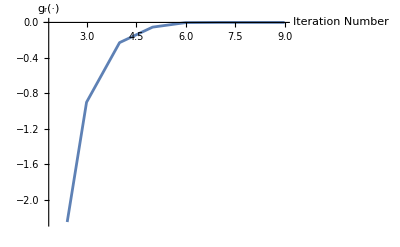

```mathematica
ListPlot[cnv,Joined->True,AxesLabel->{"Iteration Number","g_r(·)"}]
```